## Attempts with predict and classify

## Trying to use File[]

```mathematica
imagesPath = NotebookDirectory[] <> "ResistorProject/Assets/Images/";
dataPath = NotebookDirectory[] <> "ResistorProject/Assets/ResistorData/";
```

```mathematica
filesByType[type_?StringQ] := Map[
	File[#]->type&,
	FileNames[{"*.jpg", "*.png"}, dataPath <> type <> "/"]
];
```

```mathematica
makeData[] := Flatten @ Map[
	filesByType,
	StringDrop[
		Select[FileNames["*",dataPath], DirectoryQ],
		StringLength[dataPath]
	]
];
```

```mathematica
data = RandomSample[makeData[]];
```

```mathematica
data[[1]]
```

File[/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/ResistorData/22/20170703_172109.png]→22

```mathematica
Length[data]
```

617

```mathematica
trainingData = data[[;;150]];
testData = data[[151;;]];
```

```mathematica
getAllImages[x_]:=Map[
Import[Keys[{#}][[1]]]->ToExpression[Values[{#}][[1]]]&,
x
];
```

```mathematica
trainingSet = getAllImages[trainingData];
testSet = getAllImages[testData];
```

```mathematica
trainingSet[[1]]
```

-Graphics-→22

```mathematica
cNoParameters = Classify[trainingSet, PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
img = -Graphics-;
```

```mathematica
cNoParameters[resistorCrop[img],"Probabilities"]
```

<|10→0.000900075,22→0.00307929,470→0.00649393,1000→0.000794327,2200→0.000323417,4700→0.115586,47000→0.00924383,220000→0.863579|>

```mathematica
mask=DeleteSmallComponents[Binarize[ColorNegate@img,0.5]];
ans = ImageRotate[ImageTrim[img,#[[1]],20],#[[2]]+Pi/2,"SameRatioCropping"]&/@ComponentMeasurements[mask,{"BoundingBox","Orientation"}][[All,2]];
```

```mathematica
ans
```

{-Graphics-}

```mathematica
cNoParameters[ans,"Probabilities"]
```

{<|10→0.0075876,22→0.000166425,470→0.00111723,1000→0.829381,2200→0.0829771,4700→0.0295297,47000→0.0457802,220000→0.00346049|>}

```mathematica
ClassifierInformation[cNoParameters]
```

Classifier information
Method | Logistic regression
Number of classes | 8
Number of features | 1
Number of training examples | 150
L1 regularization coefficient | 0
L2 regularization coefficient | 10.

```mathematica
cNoParametersM = ClassifierMeasurements[cNoParameters, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNoParametersM["Accuracy"]
```

0.655246

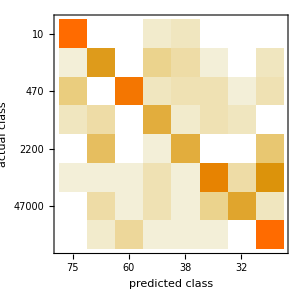

```mathematica
cNoParametersM["ConfusionMatrixPlot"]
```

```mathematica
cNeuralNet = Classify[trainingSet, Method->"NeuralNetwork", PerformanceGoal->"Quality", FeatureExtractor->"ImageFeatures"]
```

ClassifierFunction[…]

```mathematica
cNeuralNetM = ClassifierMeasurements[cNeuralNet, testSet]
```

ClassifierMeasurementsObject[…]

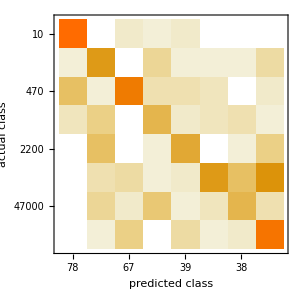

```mathematica
cNeuralNetM["ConfusionMatrixPlot"]
```

```mathematica
pNoParameters = Predict[trainingSet]
```

PredictorFunction[…]

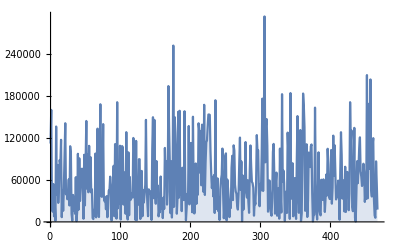

```mathematica
Show[
DiscretePlot[
Module[
{image, value},
image = Keys[testSet[[x]]];
value = Values[testSet[[x]]];
Abs[value - pNoParameters[image]]
],
{x, 1, Length[testSet], 1}
]
]
```